```mathematica
TheSize=10;
```

```mathematica
vertexRep={1->1,6->2,2->3,7->4,3->5,4->6,5->7}
```

{1→1,6→2,2→3,7→4,3→5,4→6,5→7}

```mathematica
{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,6<->2,2<->7,7<->3(*,3<->8,8<->4,4<->9,9<->5,5<->10,10<->1*)}/.vertexRep//Sort
```

{1<->2,1<->3,2<->3,3<->4,3<->5,4<->5,5<->6,6<->7,7<->1}

```mathematica
allGraphs=Association[];
g=Graph[Range[TheSize],{1<->2,1<->3,2<->3,3<->4,3<->5,4<->5,5<->6,6<->7,5<->7,7<->8,7<->9,8<->9,9<->10,9<->1,10<->1}];
```

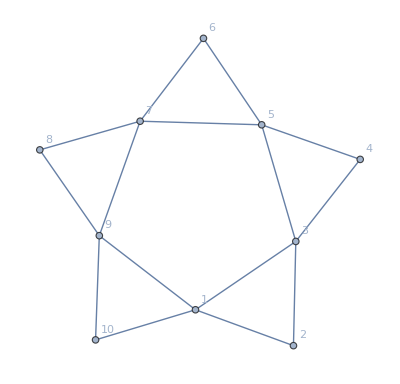

```mathematica
Graph[g,VertexLabels->"Name"]
```

```mathematica
mat = MatrixFromGraph[g]
```

{{2,1,1,0,0,0,0,0,1,1},{1,2,1,0,0,0,0,0,0,0},{1,1,2,1,1,0,0,0,0,0},{0,0,1,2,1,0,0,0,0,0},{0,0,1,1,2,1,1,0,0,0},{0,0,0,0,1,2,1,0,0,0},{0,0,0,0,1,1,2,1,1,0},{0,0,0,0,0,0,1,2,1,0},{1,0,0,0,0,0,1,1,2,1},{1,0,0,0,0,0,0,0,1,2}}

```mathematica
MatrixForm[mat]
```

(2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 2 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 2 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2)

```mathematica
FileName="d:\\Saved\\allGraphs"<>ToString[TheSize]<>".m";
If[FileExistsQ[FileName],
Print["Loading ... ", FileName];
allGraphs=Get[FileName],
Timing[Monitor[ComputeGraph[mat,32],{globalDepth,Length[allGraphs]}]];
Put[allGraphs,FileName]
];
Length[allGraphs]
```

```mathematica
TableForm[Sort[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally],TableDepth->2]
```

{3,GreaterEqual} | 5
{4,GreaterEqual} | 63
{5,Equal} | 39
{5,GreaterEqual} | 315
{6,Equal} | 273
{6,Greater} | 5
{6,GreaterEqual} | 1130
{7,Equal} | 973
{7,Greater} | 58
{7,GreaterEqual} | 3065

```mathematica
atomKeys=Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[atomKeys]
```

92

```mathematica
TableForm[Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,atomKeys]//Tally//Sort,TableDepth->2]
```

{3,GreaterEqual} | 5
{4,GreaterEqual} | 35
{5,Equal} | 39
{6,Equal} | 12
{7,Equal} | 1

```mathematica
repZero=Sort[Map[allGraphs[#,"colofour"]->0&,Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]=="Equal"&&Length[DeleteDuplicates[ListofVars[allGraphs[#,"colofour"]]]]==1&]]]
```

{v146x2x3x5x7→0,v14x25x3x6x7→0,v14x26x3x5x7→0,v14x27x3x5x6→0,v14x2x36x5x7→0,v14x2x37x5x6→0,v14x2x3x57x6→0,v14x2x3x5x6x7→0,v15x24x3x6x7→0,v15x26x3x4x7→0,v15x27x3x4x6→0,v15x2x36x4x7→0,v15x2x37x4x6→0,v15x2x3x46x7→0,v15x2x3x47x6→0,v15x2x3x4x6x7→0,v16x24x3x5x7→0,v16x25x3x4x7→0,v16x27x3x4x5→0,v16x2x37x4x5→0,v16x2x3x47x5→0,v16x2x3x4x57→0,v16x2x3x4x5x7→0,v1x246x3x5x7→0,v1x247x3x5x6→0,v1x24x36x5x7→0,v1x24x37x5x6→0,v1x24x3x57x6→0,v1x24x3x5x6x7→0,v1x257x3x4x6→0,v1x25x36x4x7→0,v1x25x37x4x6→0,v1x25x3x46x7→0,v1x25x3x47x6→0,v1x25x3x4x6x7→0,v1x26x37x4x5→0,v1x26x3x47x5→0,v1x26x3x4x57→0,v1x26x3x4x5x7→0,v1x27x36x4x5→0,v1x27x3x46x5→0,v1x27x3x4x5x6→0,v1x2x36x47x5→0,v1x2x36x4x57→0,v1x2x36x4x5x7→0,v1x2x37x46x5→0,v1x2x37x4x5x6→0,v1x2x3x46x57→0,v1x2x3x46x5x7→0,v1x2x3x47x5x6→0,v1x2x3x4x57x6→0,v1x2x3x4x5x6x7→0}

## empty graph where areth thou ?

```mathematica
empty=First[Select[Keys[allGraphs],With[{g=allGraphs[#]["graph"],sets=allGraphs[#]["vertexsets"]},VertexCount[g]==7&&EdgeCount[g]==9 &&EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]&&EdgeQ[g,3<->4]&&EdgeQ[g,5<->4]
]&]]
```

4668204241

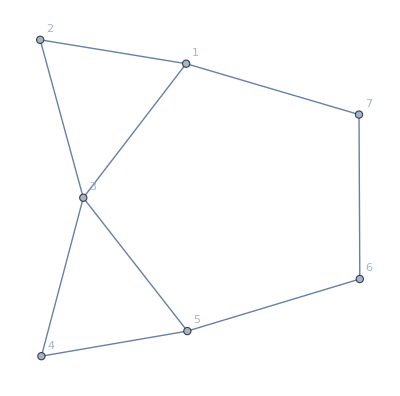

```mathematica
Graph[EdgeList[ allGraphs[empty,"graph"]],VertexLabels->"Name"]
```

## amigos have to be found too

```mathematica
Hold[EdgeQ[g,1<->2]&& EdgeQ[g,2<->3]&& EdgeQ[g,3<->4]&& EdgeQ[g,4<->5]&& EdgeQ[g,5<->1]&&EdgeQ[g,1<->3]&&EdgeQ[g,1<->4]&& EdgeQ[g,1<->6]&& EdgeQ[g,2<->6]]/.vertexRep
```

Hold[EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,1<->5]&&EdgeQ[g,1<->6]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]]

```mathematica
amigo1=First[Select[Keys[allGraphs],With[{g=allGraphs[#]["graph"],sets=allGraphs[#]["vertexsets"]},VertexCount[g]==7&&EdgeCount[g]==11 && EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,1<->5]&&EdgeQ[g,1<->6]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]
]&]]
```

4840391125

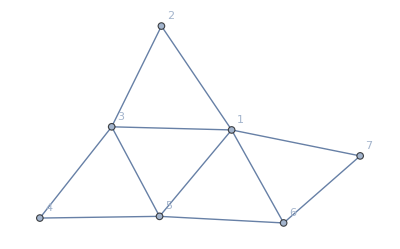

```mathematica
Graph[EdgeList[ allGraphs[amigo1,"graph"]],VertexLabels->"Name"]
```

```mathematica
Hold[EdgeQ[g,1<->2]&& EdgeQ[g,2<->3]&& EdgeQ[g,3<->4]&& EdgeQ[g,4<->5]&& EdgeQ[g,5<->1]&&EdgeQ[g,2<->4]&&EdgeQ[g,2<->5]&& EdgeQ[g,1<->6]&& EdgeQ[g,2<->6]]/.vertexRep
```

Hold[EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,3<->6]&&EdgeQ[g,3<->7]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]]

```mathematica
amigo2=First[Select[Keys[allGraphs],With[{g=allGraphs[#]["graph"],sets=allGraphs[#]["vertexsets"]},VertexCount[g]==7&&EdgeCount[g]==11 && EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,3<->6]&&EdgeQ[g,3<->7]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]
]&]]
```

4668207157

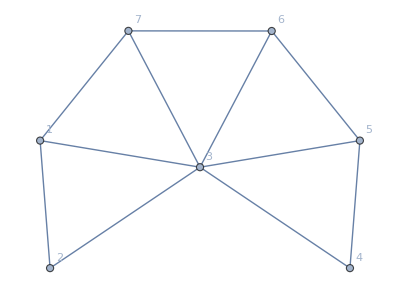

```mathematica
Graph[EdgeList[ allGraphs[amigo2,"graph"]],VertexLabels->"Name"]
```

```mathematica
Hold[EdgeQ[g,1<->2]&& EdgeQ[g,2<->3]&& EdgeQ[g,3<->4]&& EdgeQ[g,4<->5]&& EdgeQ[g,5<->1]&&EdgeQ[g,3<->5]&& EdgeQ[g,1<->6]&& EdgeQ[g,2<->6]]/.vertexRep
```

Hold[EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,5<->7]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]]

```mathematica
amigosingle1=First[Select[Keys[allGraphs],With[{g=allGraphs[#]["graph"],sets=allGraphs[#]["vertexsets"]},VertexCount[g]==7&&EdgeCount[g]==10 && EdgeQ[g,1<->3]&&EdgeQ[g,3<->5]&&EdgeQ[g,5<->6]&&EdgeQ[g,6<->7]&&EdgeQ[g,7<->1]&&EdgeQ[g,5<->7]&&EdgeQ[g,1<->2]&&EdgeQ[g,3<->2]
]&]]
```

4668204244

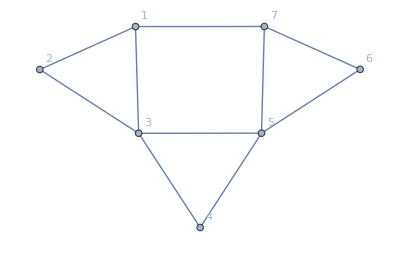

```mathematica
Graph[EdgeList[ allGraphs[amigosingle1,"graph"]],VertexLabels->"Name"]
```

## full graph where areth thou ?

```mathematica
repcolofourtextBase2=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k]],{k,atomKeys}];
```

```mathematica
Take[repcolofourtextBase2,-20]
```

{v14x2x37x5x6→v14x2x37x5x6,v14x2x36x5x7→v14x2x36x5x7,v14x2x36x57→v14x2x36x57,v14x27x3x5x6→v14x27x3x5x6,v14x27x36x5→v14x27x36x5,v14x26x3x5x7→v14x26x3x5x7,v14x26x3x57→v14x26x3x57,v14x26x37x5→v14x26x37x5,v14x25x3x6x7→v14x25x3x6x7,v14x25x37x6→v14x25x37x6,v14x25x36x7→v14x25x36x7,v14x257x3x6→v14x257x3x6,v14x257x36→v14x257x36,v146x2x3x5x7→v146x2x3x5x7,v146x2x3x57→v146x2x3x57,v146x2x37x5→v146x2x37x5,v146x27x3x5→v146x27x3x5,v146x25x3x7→v146x25x3x7,v146x25x37→v146x25x37,v146x257x3→v146x257x3}

```mathematica
repcolofourgraph2=Table[allGraphs[k,"colofour"]->Tooltip[
Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}]],
Labeled[
Column[
{
Style[k,Bold],
MatrixForm[mat,TableHeadings->{Table[Style[k,Red],{k,TheSize}],Table[Style[k,Red],{k,TheSize}]}]
,
Row[{
allGraphs[k]["graph"],
Graph[
VertexList[allGraphs[k]["graph"]],
EdgeList[allGraphs[k]["graph"]],
VertexLabels->PropertyValue[allGraphs[k]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[allGraphs[k]["children"],Italic],
Style[allGraphs[k]["colofour"]/.repcolofourtextBase2,Italic]
},
Center
],Style[allGraphs[k]["compwhy"],Bold]]
],{k,atomKeys}];
```

```mathematica
Take[repcolofourgraph2,2]
```

{v1x2x3x4x5x6x7→-Graphics-v1x2x3x4x5x6x75230176601,v1x2x3x4x57x6→-Graphics-v1x2x3x4x57x65230176604}

```mathematica
Length[repcolofourgraph2]
```

92

```mathematica
Length[DeleteDuplicates[ListofVars[2*allGraphs[empty,"colofour"]-(allGraphs[amigo1,"colofour"]+allGraphs[amigo2,"colofour"]+allGraphs[amigosingle1,"colofour"])/.repZero]]]
```

40

```mathematica
With[
{headingFormat=Style[#,Red,FontSize->11,FontFamily->"Tahoma"]&},MatrixForm[2*allGraphs[empty,"colortable"]-(allGraphs[amigo1,"colortable"]+allGraphs[amigo2,"colortable"]+allGraphs[amigosingle1,"colortable"])//Simplify,TableHeadings->{Map[headingFormat[#[[1]]<->#[[2]]]&,Subsets[Range[TheSize],{2}]],Map[ headingFormat,{"=","≠"}]}]/.repZero/.repcolofourgraph2]
```

```mathematica
(*Graph[DependencyGraph[allGraphs,empty],GraphLayout->"LayeredDigraphEmbedding"]*)
```

```mathematica
With[
{headingFormat=Style[#,Red,FontSize->11,FontFamily->"Tahoma"]&},MatrixForm[allGraphs[empty,"colortable"]//Simplify,TableHeadings->{Map[headingFormat[#[[1]]<->#[[2]]]&,Subsets[Range[TheSize],{2}]],Map[ headingFormat,{"=","≠"}]}]/.repZero/.repcolofourgraph2]
```

```mathematica
allGraphs[empty,"compwhy"]/.repcolofourgraph2
```

This is a planar contraction

```mathematica
allGraphs[4826272572,"compwhy"]/.repcolofourgraph2
```

Missing[KeyAbsent,4826272572]

```mathematica
allGraphs[4854970390,"compwhy"]/.repcolofourgraph2
```

Missing[KeyAbsent,4854970390]

```mathematica
allGraphs[4855501831,"compwhy"]/.repcolofourgraph2
```

Missing[KeyAbsent,4855501831]

```mathematica
allGraphs[4855514953,"compwhy"]/.repcolofourgraph2
```

Missing[KeyAbsent,4855514953]

```mathematica
allGraphs[4855519426,"compwhy"]/.repcolofourgraph2
```

Missing[KeyAbsent,4855519426]

```mathematica
allGraphs[4855519426,"graph"]
```

Missing[KeyAbsent,4855519426]

```mathematica
MyPlanar[allGraphs,empty]
```

True

```mathematica
empty
```

4668204241

## inequalities have to be computed for 7 nodes

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsPure]
```

5926

```mathematica
ineqsPureAnd=Fold[And,ineqsPure];
```

We can remove any eqaution of the for x1+x2 +... >=0 since that doesn’t really add any information

```mathematica
trivial=Length[Select[ineqsPure,Length[#[[1]]]≠1&&#[[0]]==GreaterEqual&]]
```

4578

```mathematica
interestingPure=Select[ineqsPure,Length[#[[1]]]==1||ToString[#[[0]]]≠"GreaterEqual"&];Length[interestingPure]
```

1348

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsPure,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]]
```

{v1x2x3x4x5x6x7→0,v1x2x3x4x57x6→0,v1x2x3x47x5x6→0,v1x2x3x46x5x7→0,v1x2x3x46x57→0,v1x2x37x4x5x6→0,v1x2x37x46x5→0,v1x2x36x4x5x7→0,v1x2x36x4x57→0,v1x2x36x47x5→0,v1x27x3x4x5x6→0,v1x27x3x46x5→0,v1x27x36x4x5→0,v1x26x3x4x5x7→0,v1x26x3x4x57→0,v1x26x3x47x5→0,v1x26x37x4x5→0,v1x25x3x4x6x7→0,v1x25x3x47x6→0,v1x25x3x46x7→0,v1x25x37x4x6→0,v1x25x36x4x7→0,v1x257x3x4x6→0,v1x24x3x5x6x7→0,v1x24x3x57x6→0,v1x24x37x5x6→0,v1x24x36x5x7→0,v1x247x3x5x6→0,v1x246x3x5x7→0,v16x2x3x4x5x7→0,v16x2x3x4x57→0,v16x2x3x47x5→0,v16x2x37x4x5→0,v16x27x3x4x5→0,v16x25x3x4x7→0,v16x24x3x5x7→0,v15x2x3x4x6x7→0,v15x2x3x47x6→0,v15x2x3x46x7→0,v15x2x37x4x6→0,v15x2x36x4x7→0,v15x27x3x4x6→0,v15x26x3x4x7→0,v15x24x3x6x7→0,v14x2x3x5x6x7→0,v14x2x3x57x6→0,v14x2x37x5x6→0,v14x2x36x5x7→0,v14x27x3x5x6→0,v14x26x3x5x7→0,v14x25x3x6x7→0,v146x2x3x5x7→0}

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
t[e_]:=Reduce[e,x,Integers]
```

```mathematica
countDone
```

0

```mathematica
atomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,atomKeys}]
```

{v1x2x3x4x5x6x7==0,v1x2x3x4x57x6==0,v1x2x3x47x5x6==0,v1x2x3x46x5x7==0,v1x2x3x46x57==0,v1x2x37x4x5x6==0,v1x2x37x46x5==0,v1x2x36x4x5x7==0,v1x2x36x4x57==0,v1x2x36x47x5==0,v1x27x3x4x5x6==0,v1x27x3x46x5==0,v1x27x36x4x5==0,v1x26x3x4x5x7==0,v1x26x3x4x57==0,v1x26x3x47x5==0,v1x26x37x4x5==0,v1x25x3x4x6x7==0,v1x25x3x47x6==0,v1x25x3x46x7==0,v1x25x37x4x6==0,v1x25x37x46≥0,v1x25x36x4x7==0,v1x25x36x47≥0,v1x257x3x4x6==0,v1x257x3x46≥0,v1x257x36x4≥0,v1x24x3x5x6x7==0,v1x24x3x57x6==0,v1x24x37x5x6==0,v1x24x36x5x7==0,v1x24x36x57≥0,v1x247x3x5x6==0,v1x247x36x5≥0,v1x246x3x5x7==0,v1x246x3x57≥0,v1x246x37x5≥0,v16x2x3x4x5x7==0,v16x2x3x4x57==0,v16x2x3x47x5==0,v16x2x37x4x5==0,v16x27x3x4x5==0,v16x25x3x4x7==0,v16x25x3x47≥0,v16x25x37x4≥0,v16x257x3x4≥0,v16x24x3x5x7==0,v16x24x3x57≥0,v16x24x37x5≥0,v16x247x3x5≥0,v15x2x3x4x6x7==0,v15x2x3x47x6==0,v15x2x3x46x7==0,v15x2x37x4x6==0,v15x2x37x46≥0,v15x2x36x4x7==0,v15x2x36x47≥0,v15x27x3x4x6==0,v15x27x3x46≥0,v15x27x36x4≥0,v15x26x3x4x7==0,v15x26x3x47≥0,v15x26x37x4≥0,v15x24x3x6x7==0,v15x24x37x6≥0,v15x24x36x7≥0,v15x247x3x6≥0,v15x247x36≥0,v15x246x3x7≥0,v15x246x37≥0,v14x2x3x5x6x7==0,v14x2x3x57x6==0,v14x2x37x5x6==0,v14x2x36x5x7==0,v14x2x36x57≥0,v14x27x3x5x6==0,v14x27x36x5≥0,v14x26x3x5x7==0,v14x26x3x57≥0,v14x26x37x5≥0,v14x25x3x6x7==0,v14x25x37x6≥0,v14x25x36x7≥0,v14x257x3x6≥0,v14x257x36≥0,v146x2x3x5x7==0,v146x2x3x57≥0,v146x2x37x5≥0,v146x27x3x5≥0,v146x25x3x7≥0,v146x25x37≥0,v146x257x3≥0}

```mathematica
assocComp=Association[];Table[assocComp[allGraphs[k,"colofour"]]=If[ToString[allGraphs[k,"comp"]]=="GreaterEqual",1,0],{k,atomKeys}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,1,0,1,1,1,0,0,0,0,1,0,1,0,1,1,0,1,1,0,1,1,1,1,1,1,0,0,0,0,1,0,1,0,1,1,0,1,1,1,1,0,1,1,1,1,1,1}

```mathematica
ExpWeight[exp_]:=Product[assocComp[var],{var,ListofVars[exp]}]
```

```mathematica
Length[atomFacts]
```

92

```mathematica
Sort[atomFacts]//TableForm
```

v146x2x3x5x7==0
v14x25x3x6x7==0
v14x26x3x5x7==0
v14x27x3x5x6==0
v14x2x36x5x7==0
v14x2x37x5x6==0
v14x2x3x57x6==0
v14x2x3x5x6x7==0
v15x24x3x6x7==0
v15x26x3x4x7==0
v15x27x3x4x6==0
v15x2x36x4x7==0
v15x2x37x4x6==0
v15x2x3x46x7==0
v15x2x3x47x6==0
v15x2x3x4x6x7==0
v16x24x3x5x7==0
v16x25x3x4x7==0
v16x27x3x4x5==0
v16x2x37x4x5==0
v16x2x3x47x5==0
v16x2x3x4x57==0
v16x2x3x4x5x7==0
v1x246x3x5x7==0
v1x247x3x5x6==0
v1x24x36x5x7==0
v1x24x37x5x6==0
v1x24x3x57x6==0
v1x24x3x5x6x7==0
v1x257x3x4x6==0
v1x25x36x4x7==0
v1x25x37x4x6==0
v1x25x3x46x7==0
v1x25x3x47x6==0
v1x25x3x4x6x7==0
v1x26x37x4x5==0
v1x26x3x47x5==0
v1x26x3x4x57==0
v1x26x3x4x5x7==0
v1x27x36x4x5==0
v1x27x3x46x5==0
v1x27x3x4x5x6==0
v1x2x36x47x5==0
v1x2x36x4x57==0
v1x2x36x4x5x7==0
v1x2x37x46x5==0
v1x2x37x4x5x6==0
v1x2x3x46x57==0
v1x2x3x46x5x7==0
v1x2x3x47x5x6==0
v1x2x3x4x57x6==0
v1x2x3x4x5x6x7==0
v146x257x3≥0
v146x25x37≥0
v146x25x3x7≥0
v146x27x3x5≥0
v146x2x37x5≥0
v146x2x3x57≥0
v14x257x36≥0
v14x257x3x6≥0
v14x25x36x7≥0
v14x25x37x6≥0
v14x26x37x5≥0
v14x26x3x57≥0
v14x27x36x5≥0
v14x2x36x57≥0
v15x246x37≥0
v15x246x3x7≥0
v15x247x36≥0
v15x247x3x6≥0
v15x24x36x7≥0
v15x24x37x6≥0
v15x26x37x4≥0
v15x26x3x47≥0
v15x27x36x4≥0
v15x27x3x46≥0
v15x2x36x47≥0
v15x2x37x46≥0
v16x247x3x5≥0
v16x24x37x5≥0
v16x24x3x57≥0
v16x257x3x4≥0
v16x25x37x4≥0
v16x25x3x47≥0
v1x246x37x5≥0
v1x246x3x57≥0
v1x247x36x5≥0
v1x24x36x57≥0
v1x257x36x4≥0
v1x257x3x46≥0
v1x25x36x47≥0
v1x25x37x46≥0

```mathematica
interestingPureAnd=Fold[And,interestingPure];
```

```mathematica
%303
```

1
 |  |  |  |

```mathematica
simplifiedPure=Monitor[Simplify[interestingPureAnd,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->atomFacts],countDone];Length[simplifiedPure]
```

63

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[#]&,AndToTable[simplifiedPure]]]]//Sort
```

{v146x257x3,v146x25x37,v146x25x3x7,v146x27x3x5,v146x2x37x5,v146x2x3x57,v14x257x36,v14x257x3x6,v14x25x36x7,v14x25x37x6,v14x26x37x5,v14x26x3x57,v14x27x36x5,v14x2x36x57,v15x246x37,v15x246x3x7,v15x247x36,v15x247x3x6,v15x24x36x7,v15x24x37x6,v15x26x37x4,v15x26x3x47,v15x27x36x4,v15x27x3x46,v15x2x36x47,v15x2x37x46,v16x247x3x5,v16x24x37x5,v16x24x3x57,v16x257x3x4,v16x25x37x4,v16x25x3x47,v1x246x37x5,v1x246x3x57,v1x247x36x5,v1x24x36x57,v1x257x36x4,v1x257x3x46,v1x25x36x47,v1x25x37x46}

```mathematica
simplifiedPureTable=AndToTable[simplifiedPure];
```

```mathematica
Take[simplifiedPure,1]/.repcolofourtextBase2
```

v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0

```mathematica
Select[Keys[allGraphs],MemberQ[ListofVars[allGraphs[#,"colofour"]],v13x25x4x6x7]&]
```

{}

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[allGraphs[#,"colofour"]]&,Keys[allGraphs]]]]//Sort
```

{v146x257x3,v146x25x37,v146x25x3x7,v146x27x3x5,v146x2x37x5,v146x2x3x57,v146x2x3x5x7,v14x257x36,v14x257x3x6,v14x25x36x7,v14x25x37x6,v14x25x3x6x7,v14x26x37x5,v14x26x3x57,v14x26x3x5x7,v14x27x36x5,v14x27x3x5x6,v14x2x36x57,v14x2x36x5x7,v14x2x37x5x6,v14x2x3x57x6,v14x2x3x5x6x7,v15x246x37,v15x246x3x7,v15x247x36,v15x247x3x6,v15x24x36x7,v15x24x37x6,v15x24x3x6x7,v15x26x37x4,v15x26x3x47,v15x26x3x4x7,v15x27x36x4,v15x27x3x46,v15x27x3x4x6,v15x2x36x47,v15x2x36x4x7,v15x2x37x46,v15x2x37x4x6,v15x2x3x46x7,v15x2x3x47x6,v15x2x3x4x6x7,v16x247x3x5,v16x24x37x5,v16x24x3x57,v16x24x3x5x7,v16x257x3x4,v16x25x37x4,v16x25x3x47,v16x25x3x4x7,v16x27x3x4x5,v16x2x37x4x5,v16x2x3x47x5,v16x2x3x4x57,v16x2x3x4x5x7,v1x246x37x5,v1x246x3x57,v1x246x3x5x7,v1x247x36x5,v1x247x3x5x6,v1x24x36x57,v1x24x36x5x7,v1x24x37x5x6,v1x24x3x57x6,v1x24x3x5x6x7,v1x257x36x4,v1x257x3x46,v1x257x3x4x6,v1x25x36x47,v1x25x36x4x7,v1x25x37x46,v1x25x37x4x6,v1x25x3x46x7,v1x25x3x47x6,v1x25x3x4x6x7,v1x26x37x4x5,v1x26x3x47x5,v1x26x3x4x57,v1x26x3x4x5x7,v1x27x36x4x5,v1x27x3x46x5,v1x27x3x4x5x6,v1x2x36x47x5,v1x2x36x4x57,v1x2x36x4x5x7,v1x2x37x46x5,v1x2x37x4x5x6,v1x2x3x46x57,v1x2x3x46x5x7,v1x2x3x47x5x6,v1x2x3x4x57x6,v1x2x3x4x5x6x7}

```mathematica
ExpressionToTable[simplifiedPureTable]/.repcolofourtextBase2
```

v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47>0
v146x257x3+v146x2x3x57+v14x257x36+v14x257x3x6+v14x26x3x57+v14x2x36x57+v16x24x3x57+v16x257x3x4+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46>0
v14x257x36+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x24x36x7+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v146x25x37+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5>0
v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46>0
v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x3x6+v14x26x3x57+v15x246x3x7+v15x247x3x6+v15x26x3x47+v15x27x3x46+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x246x3x57+v1x257x3x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x257x3x46+v1x25x37x46>0
v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v16x24x3x57+v16x257x3x4+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46>0
v146x25x3x7+v146x27x3x5+v14x25x36x7+v14x27x36x5+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v16x247x3x5+v16x25x3x47+v1x247x36x5+v1x25x36x47>0
v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v1x246x37x5+v1x247x36x5>0
v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x27x3x46+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46>0
v14x257x3x6+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x247x3x6+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x3x46+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x257x3x46+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x27x3x46+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46>0
v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x37x46+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x2x36x47+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v146x25x37+v146x25x3x7+v146x2x37x5+v146x2x3x57+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x25x37x4+v1x246x37x5+v1x246x3x57+v1x25x37x46>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v15x247x3x6+v15x24x37x6+v15x27x3x46+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x257x3x46+v1x25x37x46>0
v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v14x26x37x5+v14x26x3x57+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x257x3x46+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x2x36x47+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x3x7+v15x24x36x7+v15x27x36x4+v15x27x3x46+v16x24x3x57+v16x257x3x4+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46>0
v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x247x3x6+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x3x46+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x25x37x46>0
v146x27x3x5+v146x2x37x5+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v1x246x37x5+v1x247x36x5>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46>0
v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x27x36x4+v15x27x3x46+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46>0
v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57>0
v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x36x47+v15x2x37x46+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x25x36x47+v1x25x37x46>0
v146x25x37+v146x25x3x7+v146x2x37x5+v146x2x3x57+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x27x36x4+v15x2x36x47+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v146x25x37+v146x25x3x7+v146x2x37x5+v146x2x3x57+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x2x36x57+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x25x37x4+v1x246x37x5+v1x246x3x57+v1x24x36x57+v1x25x37x46>0
v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x27x3x46+v15x2x36x47+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x27x3x46+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v1x246x37x5+v1x246x3x57+v1x257x3x46+v1x25x37x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v1x246x37x5+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x2x36x47+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47>0
v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57>0
v146x25x37+v146x25x3x7+v146x2x37x5+v146x2x3x57+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x2x36x57+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x36x47+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x24x36x57+v1x25x36x47+v1x25x37x46>0
v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x247x3x6+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x3x46+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x257x3x46+v1x25x37x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46>0
v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x27x36x4+v15x27x3x46+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v1x246x37x5+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x37x46>0
v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46>0

```mathematica
expList=Map[First,simplifiedPureTable];Length[expList]
```

63

```mathematica
ExpressionsToGraph6[list_]:=Block[{result={},left,newNode=-1,currentBis,vertexLabels, vertices={},key,mat2,vertexStyle={},vertexLabels2={},vertexStyle2={},sumKey,crit},
Table[
If[Length[current]==0,
result=Append[result,current->newNode ],

currentBis=current;
crit = Fold[Plus,current];
sumKey=First[Select[Keys[allGraphs],(allGraphs[#,"colofour"]==crit)/.repZero&]];
newNode=sumKey;
vertexLabels2=Append[vertexLabels2,sumKey->allGraphs[sumKey,"graph"]];
vertexStyle2=Append[vertexStyle2,sumKey->ColourForKey[allGraphs,sumKey]];
Table[
result=Append[result,currentBis[[k]]->newNode];
vertices=Append[vertices,currentBis[[k]]]
,{k,Length[currentBis]}
];
];

(*result=Append[result,newNode->0];*)
newNode=newNode-1
,
{current,list}
];
vertices = DeleteDuplicates[vertices];
vertexLabels=Table[key=Select[Keys[allGraphs],allGraphs[#,"colofour"]==v&]//First;
mat2=allGraphs[key,"matrix"];
v->Tooltip[
Labeled[
allGraphs[key]["graph"],allGraphs[key]["colofour"]],
Labeled[
Column[
{
Style[key,Bold],
MatrixForm[mat2,TableHeadings->{Table[Style[k,Red],{k,TheSize}],Table[Style[k,Red],{k,TheSize}]}]
,
Row[{
allGraphs[key]["graph"],
Graph[
VertexList[allGraphs[key]["graph"]],
EdgeList[allGraphs[key]["graph"]],
VertexLabels->PropertyValue[allGraphs[key]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[allGraphs[key]["parents"],Italic],
Style[allGraphs[key]["colofour"],Italic]
},
Center
],Style[allGraphs[key]["compwhy"],Bold]]]

,{v,vertices}];
vertexStyle=Table[key=Select[Keys[allGraphs],allGraphs[#,"colofour"]==v&]//First;v->ColourForKey[allGraphs,key],{v,vertices}];
Graph[result,VertexLabels->Join[vertexLabels,vertexLabels2],VertexStyle->Join[vertexStyle,vertexStyle2]]
]
```

```mathematica
simple=Select[expList,Length[#]≤20&&ExpWeight[#]>0&]
```

{v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v1x246x37x5+v1x247x36x5,v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46,v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46,v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47,v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x257x3x46+v1x25x37x46,v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v14x26x37x5+v14x26x3x57+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x257x3x46+v1x25x37x46,v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47,v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v16x24x3x57+v16x257x3x4+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46,v146x257x3+v146x2x3x57+v14x257x36+v14x257x3x6+v14x26x3x57+v14x2x36x57+v16x24x3x57+v16x257x3x4+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46,v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46,v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x247x36x5+v1x24x36x57,v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5,v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47+v1x25x37x46,v14x257x36+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x24x36x7+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x27x3x46+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47,v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v14x257x3x6+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x247x3x6+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x3x46+v15x2x37x46+v1x246x37x5+v1x246x3x57+v1x257x3x46+v1x25x37x46,v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v1x246x3x57+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x257x3x46+v1x25x36x47,v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v14x257x36+v14x257x3x6+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x2x36x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v1x246x37x5+v1x247x36x5+v1x25x36x47+v1x25x37x46,v146x27x3x5+v146x2x37x5+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v15x2x37x46+v16x247x3x5+v16x24x37x5+v1x246x37x5+v1x247x36x5,v146x257x3+v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v146x2x3x57+v14x257x3x6+v14x25x37x6+v15x247x3x6+v15x24x37x6+v15x27x3x46+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x24x3x57+v16x257x3x4+v16x25x37x4+v16x25x3x47+v1x257x3x46+v1x25x37x46,v14x257x36+v14x257x3x6+v14x25x36x7+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x27x36x4+v15x2x36x47+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v146x25x37+v146x25x3x7+v146x2x37x5+v146x2x3x57+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x246x3x57+v1x25x37x46,v146x25x37+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46,v146x25x37+v146x25x3x7+v146x2x37x5+v146x2x3x57+v14x25x37x6+v14x26x37x5+v14x26x3x57+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x24x3x57+v16x25x37x4+v1x246x37x5+v1x246x3x57+v1x25x37x46,v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46,v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x37x46+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x25x37x46,v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46,v146x25x37+v146x25x3x7+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x2x36x47+v15x2x37x46+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x25x36x47+v1x25x37x46,v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x3x6+v14x26x3x57+v15x246x3x7+v15x247x3x6+v15x26x3x47+v15x27x3x46+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x246x3x57+v1x257x3x46,v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x24x37x6+v15x26x37x4+v15x27x3x46+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46,v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x37x6+v14x26x37x5+v15x246x37+v15x246x3x7+v15x247x3x6+v15x24x37x6+v15x26x37x4+v15x26x3x47+v15x27x3x46+v15x2x37x46+v16x247x3x5+v16x24x37x5+v16x25x37x4+v16x25x3x47+v1x246x37x5+v1x25x37x46,v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x2x36x47+v16x247x3x5+v16x24x3x57+v16x257x3x4+v16x25x3x47+v1x247x36x5+v1x24x36x57+v1x257x36x4+v1x25x36x47,v146x257x3+v146x25x3x7+v146x27x3x5+v146x2x3x57+v14x257x36+v14x257x3x6+v14x25x36x7+v14x26x3x57+v14x27x36x5+v14x2x36x57+v15x246x3x7+v15x24x36x7+v15x27x36x4+v15x27x3x46+v16x24x3x57+v16x257x3x4+v1x246x3x57+v1x24x36x57+v1x257x36x4+v1x257x3x46,v146x25x3x7+v146x27x3x5+v14x25x36x7+v14x27x36x5+v15x246x3x7+v15x247x36+v15x247x3x6+v15x24x36x7+v15x26x3x47+v15x27x36x4+v15x27x3x46+v15x2x36x47+v16x247x3x5+v16x25x3x47+v1x247x36x5+v1x25x36x47,v146x25x37+v146x25x3x7+v146x27x3x5+v146x2x37x5+v14x25x36x7+v14x25x37x6+v14x26x37x5+v14x27x36x5+v15x246x37+v15x246x3x7+v15x24x36x7+v15x24x37x6+v15x26x37x4+v15x27x36x4+v15x27x3x46+v15x2x37x46+v16x24x37x5+v16x25x37x4+v1x246x37x5+v1x25x37x46}

```mathematica
Length[expList]
```

63

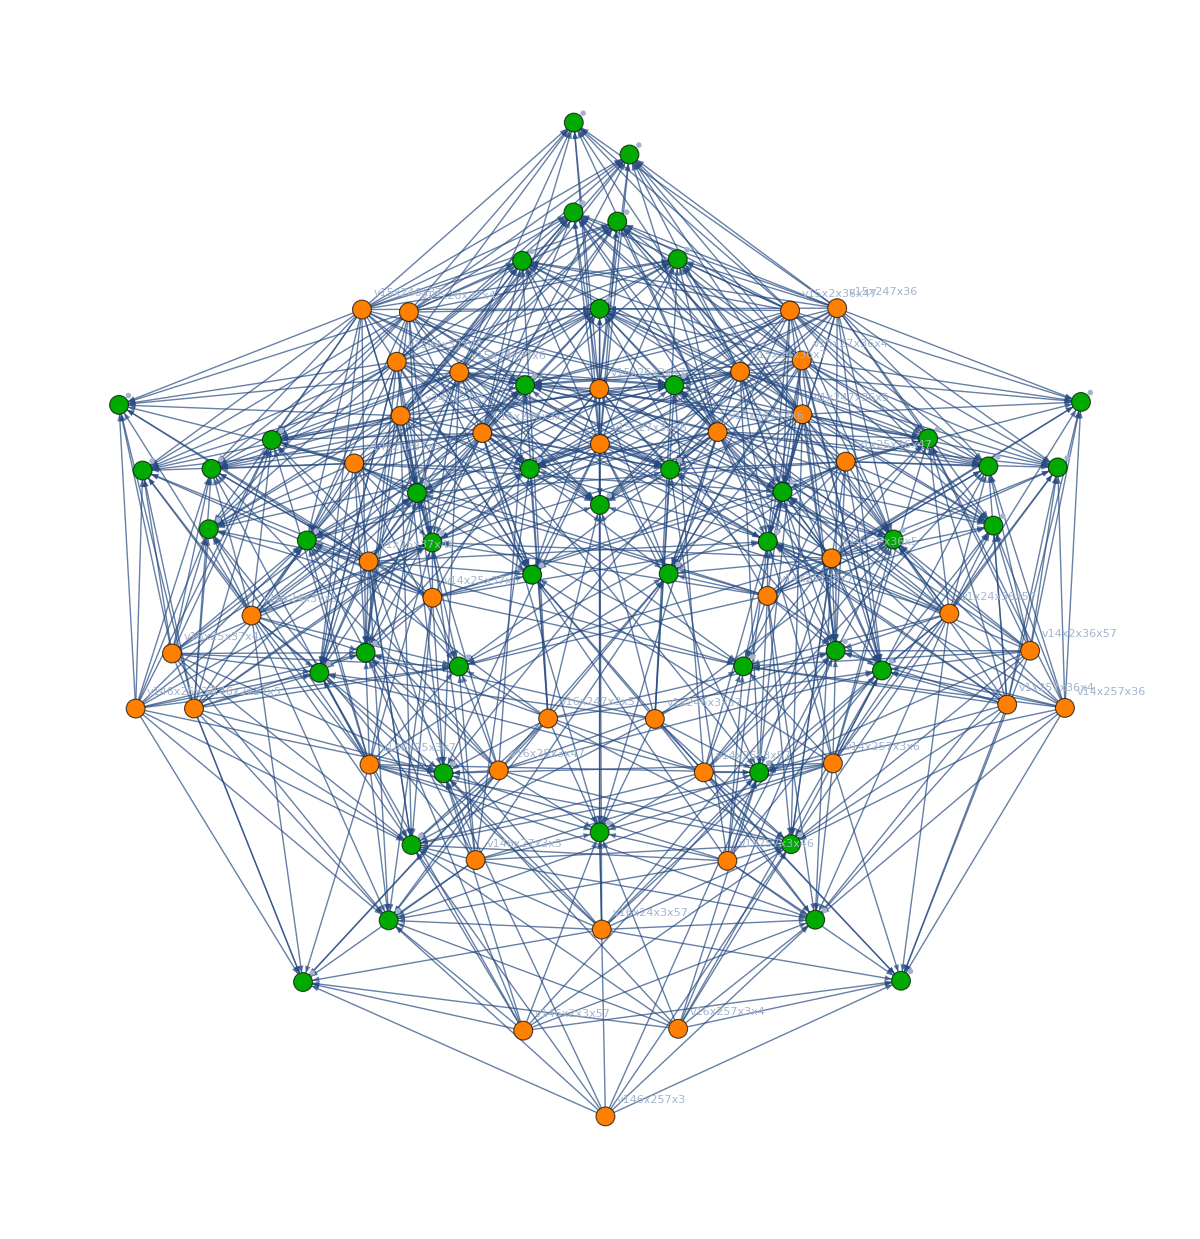

```mathematica
Graph[ExpressionsToGraph6[simple],ImageSize->1200]
```